```mathematica
eqn = y[x] == x^2 +∫_0^x (x-s)*y[s]ⅆs;
sol=DSolveValue[eqn,y[x],x]
```

2 (-1+Cosh[x])

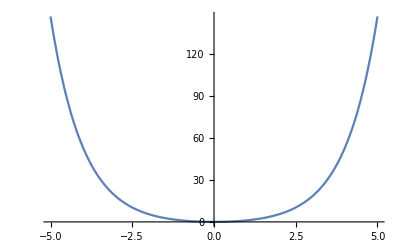

```mathematica
Plot[sol,{x,-5,5}]
```